## Решение задачи штейнера на больших графах

#### Фёдор Курмазов, ПМ-2041

## Задача штейнера на графе.

#### Steiner tree problem in graphs (STP):

Для данного взвешенного неориентированного графа G=(V,E) и множества терминалов T⊆V, требуется найти остовный подграф S графа G наименьшего веса, стягивающий множество T.

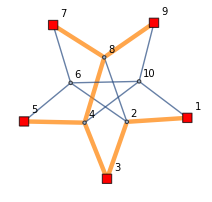

#### Сложность решения :

Задача разрешимости соответствующая STP является NP-полной.

Оптимизационная версия STP является NP-сложной.

Метрическая STP является APX-полной.

## Организация работ

#### Структура проекта:

```mathematica
-Graphics-            -Graphics-
```

## Реализованные алгоритмы

#### Точные решения :

(DW) Алгоритм Дрейфуса-Вагнера.						O(3^t n+2^t n^2)

#### Приближенные :

(DNH)   2-приближение, алгоритм Коу-Марковского-Бермана. 	     	O(t m log(n))

(DNHA) 2-приближение, алгоритм Мельхорна. 	    			O(m log(n))

#### Жадные :

(SPH) Добавление кратчайшего пути						O(n m log(n))

(RSPH) Повторный SPH.							O(n m log(n))

#### Локальный поиск:

(VI) Вставка вершины штейнера. 						O((n - |S|) m log(n))

(VE) Удаление вершины штейнера. 						O(|S| m log(n))

(PE) Обмен ключевыми путями. 						O(m log(n))

## Алгоритм Дрейфуса-Вагнера

Точное решение. Динамическое программирование.

Задача решается для подмножества терминалов исходя из решений для подмножеств меньшего размера. Всего подмножеств у подмножеств 3^t.

Алгоритм пытается склеить два дерева штейнера лучшим способом.

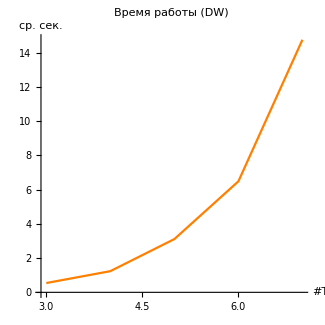

## Жадные алгоритмы

#### Добавление кратчайшего пути:

Алгоритм начинает с вершины - терминала.

На каждой итерации добавляет в текущее решение путь до близжайшего терминала.

```mathematica
greedyAnim
```

## 2-приближение

#### Алгоритм Коу-Марковского-Бермана:

1. Построить метрическое замыкание G^* индуцированного графа G[T].

2. Найти в G^* минимальное остовное дерево.

3. Найти соответствующие ему пути в G.

4. Найти минимальное остовное дерево графа из полученных путей и почистить граф от ветвей без терминалов.

#### Время работы:

На 1-ом шаге, для построение метрического замыкания графа, алгоритм вычисляет кратчайшие пути от каждого терминала t∈T до остальных терминалов.

Это занимает O(|T|m log(n)), что плохо при большом количестве терминалов.

#### Алгоритм Мельхорна:

Цель - ускорить первый шаг алгоритма до O(m log n).

Вместо пересчета расстояния от каждой вершины до каждой можно построить диаграмму Вороного.

## Диаграммы Вороного

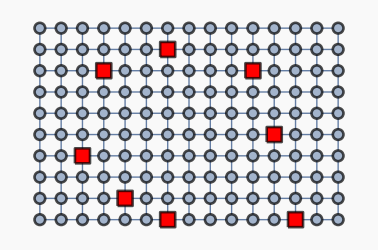
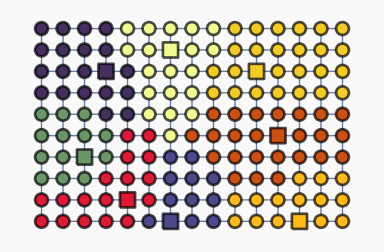
```mathematica
-Graphics-     ->     -Graphics-
```

Множество вершин V разбивается на подмножества относительно заданного множества вершин-центров C ⊆ V так, что вершина u относится к множеству ближайшего центра.

Диаграму можно построить за O(m log n), используя алгоритм Дейкстры.

#### Алгоритм Мельхорна:

По граничным ребрам диаграммы востанавливаются пути между терминалами. В графе этих путей находится минимальное остовное дерево.

Это дерево соответствует дереву в G^*.

## Локальный поиск.

Опр. Для S - допустимого решения задачи вершиной штейнера называется u ∈ S, u ∉ T.

#### Вставка вершины штейнера:

Перебор всех вершин графа, вне S.

Происходит попытка добавить вершину, и пересчитать MST.

#### Удаление вершины штейнера:

Перебор всех вершин штейнера.

Происходит попытка удалить вершину, и пересчитать MST.

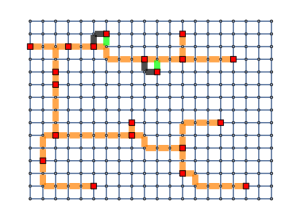
-Graphics-
Удаление вершины

```mathematica
vertElim
```

## Обмен ключевых путей.

Опр. Ключевой вершиной называется u∈S : u∈T ∨ d_S(u)≥3.

Опр. Ключевой путь в S - путь, концами которого являются ключевые вершины, а внутренние вершины ключевыми не являются.

S разбивается на ключевые пути.

Происходит попытка удалить путь, и заменить его на менее длинный.

```mathematica
kpeAnim
```

## Обмен ключевых путей.

#### Реализация:

Используются диаграмы Вороного, левосторонние кучи, СНМ.

1. Строится диаграма Вороного с центрами во всех вершинах S.

2. Для каждой вершины S создается левосторонняя куча с граничными ребрами ее зоны.

3. Граф подвешивается и обходится от листьев к корням.

4. На подъеме выявляются ключевые пути, и проверяется возможность их замены.

5. Для выбора лучшей замены диаграма Вороного чинится хитрым способом.

6. После обхода поддерева кучи в нем сливаются.

## Расчеты.

Данные взяты из библиотеки steinlib: http://steinlib.zib.de

Тестировался алгоритм Мельхорна и возможность его улучшения с помощью комбинации алгоритмов локального поиска (PE VI VE).

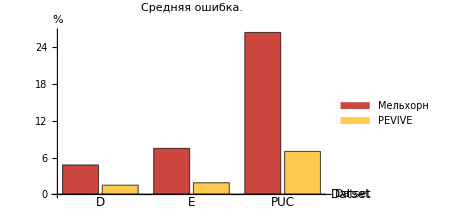
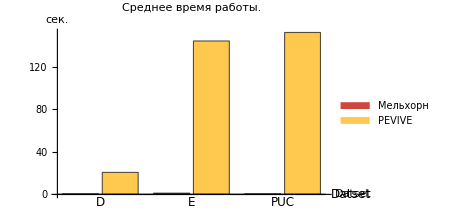
-Graphics- | -Graphics-

```mathematica
compCharts
```

```mathematica
dataInfo
```

| Состав данных |  | 
Dataset | D | E | PUC
Вершины | 1000 | 2500 | ≤4096
Ребра | ≤25000 | ≤64000 | ≤28512
Терминалы | ≤500 | ≤1250 | ≤2048

## Список источников.

[1] Корте Б. Комбинаторная оптимизация. Теория и Алгоритмы / Бернард Корте, Йенс Фиген ; перевод с англ. М.А. Бабенко ; - М. : МЦНМО ; 2015 - 720 с.

[2] Markowski G. A fast algorithm for steiner trees / G. Markowski, L. Kou, L. Berman ; 1981.

[3] Fuchs B. Speeding up the Dreyfus-Wagner Algorithmfor minimum Steiner trees / B. Fuchs, W. Kern, X. Wang ; 2007

[4] Fomin F.  Computing Optimal Steiner Trees in Polynomial Space / F. Fomin, F. Grandoni, D. Kratsch, D. Lokshtanov, S.Saurabh ; 2012

[5] Dreyfus S.  The Steiner Problem in Graphs / S. Dreyfus, R. Wagner ; 1971

[6] Plesnik J. Heuristics for the Steiner problem in graphs / J. Plesnik ; 1989

[7] Uchoa E. Fast Local Search for Steiner Trees in Graphs / E. Uchoa, R. Werneck  ; 2010

[8] Mehlhorn K. A Faster Approximation Algorithm for the Steiner Tree Problem in Graphs / K. Mehlhorn ; 1988

GitHub репозиторий: https://github.com/spefk/wolfram_steiner

## init

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"dump\\compCharts";
<<"dump\\presentation_mehlhorn_pe_grid_01";
<<"dump\\presentation_greedy";
```

```mathematica
greedyAnim :=
Animate[gridSPHFrames⟦k⟧, {k, 1, Length@gridSPHFrames, 1}, AnimationRate->1.2,ControlPlacement->Top, AppearanceElements->None, AnimationRunning->False];
```

```mathematica
kpeAnim :=
Animate[gridPEVIVEMelhornFrames⟦k⟧, {k, 1, Length@gridPEVIVEMelhornFrames, 1}, AnimationRate->0.75,ControlPlacement->Top, AppearanceElements->None, AnimationRunning->False];
```

```mathematica
vertElim = Grid[{{-Graphics-},{"Удаление вершины"}}];
```

```mathematica
dataInfo=Grid[
{
{SpanFromLeft,  Style["Состав данных", FontSize->13, FontFamily->"Roboto Slab"],SpanFromLeft},
Style[#, FontSize->13, FontFamily->"Roboto Slab"]&/@{"Dataset", "D", "E", "PUC"},
Style[#, FontSize->13, FontFamily->"Roboto Slab"]&/@{"Вершины", "1000", "2500", "≤4096"},
Style[#, FontSize->13, FontFamily->"Roboto Slab"]&/@{"Ребра", "≤25000", "≤64000", "≤28512"},
Style[#, FontSize->13, FontFamily->"Roboto Slab"]&/@{"Терминалы", "≤500", "≤1250", "≤2048"}
},
Frame->All, Spacings->{2.5,0.5}];
```

```mathematica
1+1
```

2

Результатом работы является пакет (.wl) и ноутбук (.nb) с примерами.

Основной функционал распределен по пакетам.

Для контроля версий использовались Git и GitHub.

Для редактирования .wl использовались Wolfram Mathematica и Sublime.